## Shape functions

```mathematica
ClearAll["Global`*"];

ϕ1[s_] = c1+c2*s+c3*s^2+c4*s^3;

{RR, MM}=CoefficientArrays[
{
ϕ1[0]==1, 
ϕ1'[0]==0,
ϕ1[le]==0,
ϕ1'[le]==0
},
{c1,c2,c3,c4}]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]

{c1, c2, c3, c4}=LinearSolve[MM, RR];
ϕ1[s]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
1 | le | le^2 | le^3
0 | 1 | 2 le | 3 le^2)

(1
0
0
0)

1-(3 s^2)/le^2+(2 s^3)/le^3

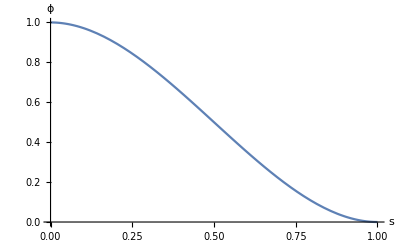

```mathematica
Plot[ϕ1[s]/.le->1, {s, 0, 1}, AxesLabel->{"s", "ϕ"}]
```

```mathematica
ClearAll[c5, c6, c7, c8, s, RR, MM];

ϕ2[s_] = c5+c6*s+c7*s^2+c8*s^3;

{RR, MM}=CoefficientArrays[
{
ϕ2[0]==0, 
ϕ2'[0]==1,
ϕ2[le]==0,
ϕ2'[le]==0
},
{c5,c6,c7,c8}]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]

{c5, c6, c7, c8}=LinearSolve[MM, RR];
ϕ2[s]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
1 | le | le^2 | le^3
0 | 1 | 2 le | 3 le^2)

(0
1
0
0)

s-(2 s^2)/le+s^3/le^2

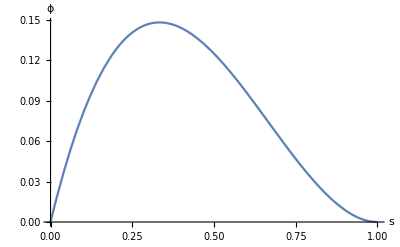

```mathematica
Plot[ϕ2[s]/.le->1, {s, 0, 1}, AxesLabel->{"s", "ϕ"}]
```

```mathematica
ClearAll[c9, c10, c11, c12, s, RR, MM];

ϕ3[s_] = c9+c10*s+c11*s^2+c12*s^3;

{RR, MM}=CoefficientArrays[
{
ϕ3[0]==0, 
ϕ3'[0]==0,
ϕ3[le]==1,
ϕ3'[le]==0
},
{c9, c10, c11, c12}]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]

{c9, c10, c11, c12}=LinearSolve[MM, RR];
ϕ3[s]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
1 | le | le^2 | le^3
0 | 1 | 2 le | 3 le^2)

(0
0
1
0)

(3 s^2)/le^2-(2 s^3)/le^3

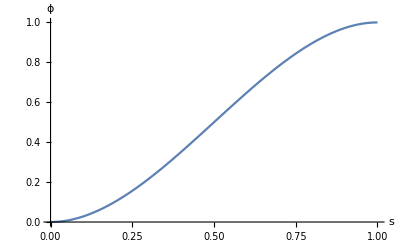

```mathematica
Plot[ϕ3[s]/.le->1, {s, 0, 1}, AxesLabel->{"s", "ϕ"}]
```

```mathematica
ClearAll[c13, c14, c15, c16, s, RR, MM];

ϕ4[s_] = c13+c14*s+c15*s^2+c16*s^3;

{RR, MM}=CoefficientArrays[
{
ϕ4[0]==0, 
ϕ4'[0]==0,
ϕ4[le]==0,
ϕ4'[le]==1
},
{c13, c14, c15, c16}]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]

{c13, c14, c15, c16}=LinearSolve[MM, RR];
ϕ4[s]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
1 | le | le^2 | le^3
0 | 1 | 2 le | 3 le^2)

(0
0
0
1)

-s^2/le+s^3/le^2

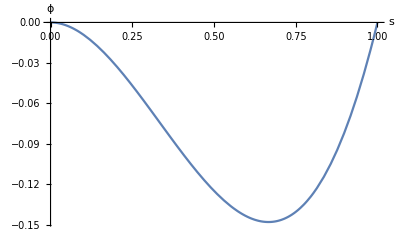

```mathematica
Plot[ϕ4[s]/.le->1, {s, 0, 1}, AxesLabel->{"s", "ϕ"}]
```

## Displacement vector

```mathematica
q = Transpose[{{q1, q2, q3, q4}}];
ϕ[s_]=Transpose[{{ϕ1[s], ϕ2[s], ϕ3[s], ϕ4[s]}}];
MatrixForm[ϕ[s]]

v[s_]= q*ϕ[s];
MatrixForm[v[s]]
```

(1-(3 s^2)/le^2+(2 s^3)/le^3
s-(2 s^2)/le+s^3/le^2
(3 s^2)/le^2-(2 s^3)/le^3
-s^2/le+s^3/le^2)

(q1 (1-(3 s^2)/le^2+(2 s^3)/le^3)
q2 (s-(2 s^2)/le+s^3/le^2)
q3 ((3 s^2)/le^2-(2 s^3)/le^3)
q4 (-s^2/le+s^3/le^2))

## Elastic stiffness matrix

```mathematica
Kel =EJe* Integrate[ϕ''[s].Transpose[ϕ''[s]], {s, 0, le}];
MatrixForm[Kel]
```

((12 EJe)/le^3 | (6 EJe)/le^2 | -(12 EJe)/le^3 | (6 EJe)/le^2
(6 EJe)/le^2 | (4 EJe)/le | -(6 EJe)/le^2 | (2 EJe)/le
-(12 EJe)/le^3 | -(6 EJe)/le^2 | (12 EJe)/le^3 | -(6 EJe)/le^2
(6 EJe)/le^2 | (2 EJe)/le | -(6 EJe)/le^2 | (4 EJe)/le)

## Geometric stiffness matrix

```mathematica
Kg = Integrate[ϕ'[s].Transpose[ϕ'[s]], {s, 0, le}];
MatrixForm[Kg]
```

(6/(5 le) | 1/10 | -6/(5 le) | 1/10
1/10 | (2 le)/15 | -1/10 | -le/30
-6/(5 le) | -1/10 | 6/(5 le) | -1/10
1/10 | -le/30 | -1/10 | (2 le)/15)

## FE stiffness matrix

```mathematica
Ke = Kel - P*Kg;
MatrixForm[Ke]
```

((12 EJe)/le^3-(6 P)/(5 le) | (6 EJe)/le^2-P/10 | -(12 EJe)/le^3+(6 P)/(5 le) | (6 EJe)/le^2-P/10
(6 EJe)/le^2-P/10 | (4 EJe)/le-(2 le P)/15 | -(6 EJe)/le^2+P/10 | (2 EJe)/le+(le P)/30
-(12 EJe)/le^3+(6 P)/(5 le) | -(6 EJe)/le^2+P/10 | (12 EJe)/le^3-(6 P)/(5 le) | -(6 EJe)/le^2+P/10
(6 EJe)/le^2-P/10 | (2 EJe)/le+(le P)/30 | -(6 EJe)/le^2+P/10 | (4 EJe)/le-(2 le P)/15)

## Nodal forces vector

```mathematica
Fe = q0*Integrate[ϕ[s], {s, 0, le}]
```

{{(le q0)/2},{(le^2 q0)/12},{(le q0)/2},{-(le^2 q0)/12}}